```mathematica
CreateFileName[filename_]:=FileNameJoin[{NotebookDirectory[], filename}];
```

```mathematica
ReplaceInRows[matrix_,oldValue_,newValue_]:=Replace[matrix,oldValue->newValue, {2}];
```

```mathematica
ExportMaxPlusMatrix[filename_, matrix_]:= Module[{m},
m = ReplaceInRows[matrix, eps, -1];
Export[CreateFileName[StringJoin[filename, ".hdf"]],m]
];
```

```mathematica
ImportMaxPlustMatrix[filename_]:= Module[{m},
m = Import[CreateFileName[StringJoin[filename, ".hdf"]],{"Datasets","Dataset1"}];
ReplaceInRows[m, -1, eps];
ReplaceInRows[m, -1., eps]
];
```

```mathematica
DataToAssociation[filename_] := 
Module[{},
data = Import[FileNameJoin[{NotebookDirectory[], filename}],"Table"];
transpose = Transpose[data];
timeData=Transpose[Rest[transpose]/. minutes_Integer:>TimeObject[{Quotient[minutes,100],Mod[minutes,100],0}]];
timeDiffTable = Table[Table[timeData[[All,j]][[i]]-timeData[[All,j]][[i-1]], {i, 2, Length[timeData]}], {j, 1, Length[Transpose[timeData]]}];
maxModeTimes = Table[Max[Commonest[timeDiffTable[[All, i]]]], {i, 1, Length[timeDiffTable[[1]]]}];
stopPairs = Table[List[First[transpose][[i-1]],First[transpose][[i]]], {i, 2, Length[maxModeTimes]+1}];
association = Association[Table[stopPairs[[i]]->maxModeTimes[[i]], {i, 1, Length[stopPairs]}]];
waiting = Association[Table[Keys[association][[i]]->
If[
(StringTake[Keys[association][[i]][[1]], -4] == "_arr" && StringTake[Keys[association][[i]][[2]], -4] == "_dep") ,
association[[Key[Keys[association][[i]]]]], Quantity[0, "Minutes"]],
{i, 1, Length[Keys[association]]}]];
travelTimeAssociation = Module[{cleaned},
cleaned = Association[];
i = 0;
While[i <Length[association],
i++;
If[waiting[[i]]==0 Quantity[, "Minutes"] && (StringTake[Keys[association][[i]][[1]], -4] == "_dep" || StringTake[Keys[association][[i]][[2]], -4] == "_arr"),
If[StringTake[Keys[association][[i]][[1]], -4] == "_dep",
AppendTo[cleaned, List[StringDrop[Keys[association][[i]][[1]], -4],Keys[association][[i]][[2]]]-> association[[Key[Keys[association][[i]]]]]],
AppendTo[cleaned, List[Keys[association][[i]][[1]],StringDrop[Keys[association][[i]][[2]], -4]]-> association[[Key[Keys[association][[i]]]]]]
],
If [waiting[[i]]==0 Quantity[, "Minutes"],
cleaned[Keys[association][[i]]] = association[[Key[Keys[association][[i]]]]],
Nothing[]],
Nothing[]];
];
cleaned
];

allStops = List[];
AppendTo[allStops, Keys[travelTimeAssociation][[1]][[1]]];
Do[AppendTo[allStops, x[[2]]],
{x, Keys[travelTimeAssociation]}
];
(*List[travelTimeAssociation, waiting, allStops]*)
travelTimeAssociation
];

SharedStops[route1_, route2_] := Intersection[Stops[route1], Stops[route2]];
```

```mathematica
x_⊕y_:=Max[x,y]
```

```mathematica
x_ ⊗y_:=x+y
```

```mathematica
eps=-Infinity
```

-∞

```mathematica
EpsilonMatrix[n_] := Table[Table[eps, {col, 1, n}], {row, 1, n}]
(* Returns an n x n matrix filled with Epsilon *)
```

```mathematica
EMatrix[n_]:= Table[Table[If[col == row, 0, eps], {col, 1, n}], {row, 1, n}]
(* Returns an n x n identity matrix *)
```

```mathematica
mplus[x_,y_]:=MapThread[Max,{x,y}, 2]
```

```mathematica
mtimes[x_,y_]:=Inner[Plus,x,y,Max]
```

```mathematica
mpower[x_,p_]:= Module[{res},
If[p>=1,
res = x,
res = EMatrix[Length[x]]];
For[i = 2, i<=p, i++,
res = mtimes[res, x]
];
res
]
```

```mathematica
mpowerDynamic[x_, p_, kpx_] := Module[{closestBelow, pow, pows},
pows = kpx;
If[p>1,
closestBelow =Max@Select[Keys[kpx],#<=p&];
pow =pows[closestBelow];
For[i = closestBelow+1, i<=p, i++,
pow = mtimes[pow, x];
AppendTo[pows, i->pow];
];,
If[p <=0,
pow=EMatrix[Length[x]],
pow=x
];
];
List[pow, pows]
]
```

```mathematica
scalarplus[x_,y_]:=Outer[Max,{x},y]
```

```mathematica
MakeNicePlaceName[rn_, s1_, s2_] :=ToString[StringJoin["p:",rn,":", s1, "+", s2]]
(* returns a formatted place name *)
```

```mathematica
MakeNiceTransitionName[rn_,q_] := ToString[StringJoin["q:",rn,":", q]]
(* returns a formatted transition name *)
```

```mathematica
MergeDirections[forward_, reverse_] := Module[{f, r, merged, nk, xS, start, end},
(* merges the forward and backward (arbitary) directions of a bus route *)
f = DataToAssociation[forward];
start = Keys[f][[1]][[1]];
r = DataToAssociation[reverse];
end = Keys[r][[1]][[1]];

Do[
nk ={StringJoin[x[[1]], If[x[[1]] ==start,"_end","_fwd"]], StringJoin[x[[2]], If[x[[2]] ==end,"_end","_fwd"]]};
f[nk] = f[x];
f[x] =.,
{x, Keys[f]}
];

Do[
nk ={StringJoin[x[[1]], If[x[[1]] ==end,"_end","_rev"]],StringJoin[x[[2]],  If[x[[2]] ==start,"_end","_rev"]]};
r[nk] = r[x];
r[x] =.,
{x, Keys[r]}
];

merged = Join[f, r];
merged
]
```

```mathematica
GetTransitionStopName[transitionString_] := StringDrop[StringSplit[transitionString, ":"][[-1]],-4];
(* returns the transition name from a "nice" formatted transition *)

GetTransitionStop[transitionString_]:=StringSplit[transitionString, ":"][[-1]];
(* returns the transition stop, including route direction from a "nice" formatted transition *)
```

```mathematica
GetTransitionRoute[transitionString_] :=StringSplit[transitionString, ":"][[2]];(* returns the transition route number from a "nice" formatted transition *)
```

```mathematica
Algorithm821[lineDataFile_, routeNumbers_]:=
(*Line data file is a list of associations, where each asscoiation corresponds to a merged version of the TT association for the forward and backward journey of a given route. So each association represents a route*)
Module[{TAPsFromRoute, Synchronization, NumberRoutes, cycleTime},
cycleTime =10 Quantity[, "Minutes"];

NumberRoutes[] := Module[{indexedAssociations},
(* returns an association with route number as key and travel time associations (route data) as values *)
indexedAssociations = Association[];
For[i=1,i<=Length[routeNumbers], i++,
indexedAssociations[routeNumbers[[i]]]= lineDataFile[[i]];
];
indexedAssociations
];

TAPsFromRoute[routeNumber_, routeAssociation_] :=Module[{startStop, endStop, cumulativeTime,nextStopCumulativeTime, modCumulative, modNextCumulative,tokens, finalHoldingTime, transitions, places, arcs},
(* returns the transitions, arcs, and place of an individual route *)
transitions = List[];
places = Association[];
arcs = List[];
startStop = Keys[routeAssociation][[1]][[1]];
endStop = Keys[routeAssociation][[-1]][[1]];
AppendTo[transitions,MakeNiceTransitionName[routeNumber, startStop]];
cumulativeTime = 0 Quantity[, "Minutes"];
Do[
AppendTo[transitions,MakeNiceTransitionName[routeNumber, pair[[2]]]];
nextStopCumulativeTime =cumulativeTime + routeAssociation[[Key[pair]]];
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(routeAssociation[[Key[pair]]] + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places,  MakeNicePlaceName[routeNumber, pair[[1]],pair[[2]]]->List[routeAssociation[[Key[pair]]], tokens]];
cumulativeTime = nextStopCumulativeTime;
AppendTo[arcs, MakeNiceTransitionName[routeNumber, pair[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[routeNumber, pair[[2]]]];
,
{pair, Keys[routeAssociation][[1;;-2]]}
];
finalHoldingTime =routeAssociation[[Key[List[endStop, StringReplace[startStop, {"fwd"->"rev"}]]]]];
nextStopCumulativeTime =cumulativeTime + finalHoldingTime;
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(finalHoldingTime + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places, MakeNicePlaceName[routeNumber,endStop, startStop]->List[finalHoldingTime, tokens] ]; (*make sure this is indeed the last one*)
AppendTo[arcs, MakeNiceTransitionName[routeNumber, endStop]->MakeNicePlaceName[routeNumber, endStop, startStop]];
AppendTo[arcs, MakeNicePlaceName[routeNumber, endStop, startStop]->MakeNiceTransitionName[routeNumber, startStop]];
List[transitions, arcs, places]
];

Synchronization[routePlaces_] := Module[{arcs, places, indexedRoutes},
(* returns the arcs and places between routes with shared stops *)
indexedRoutes = NumberRoutes[];
arcs=List[];
places=Association[];
Do[
Do[
Do[
Do[
If[assoc1 != assoc2,
If[StringDrop[key1[[2]],-4]==StringDrop[key2[[2]],-4],
(* add arc from previous stop on origin line to new place *)
(* add arc from new place to shared stop on the other line *)
placeWeWant = MakeNicePlaceName[assoc2, key2[[1]], key2[[2]] ];
AppendTo[places, MakeNicePlaceName[StringJoin[assoc2, "->", assoc1], key2[[1]], key1[[2]]]->routePlaces[[placeWeWant]]];
AppendTo[arcs, MakeNiceTransitionName[assoc2,key2[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[assoc1, key1[[2]]]];,
Nothing[]
];
Nothing[]
];,
{key2,Keys[indexedRoutes[[Key[assoc2]]]]}
],
{key1,Keys[indexedRoutes[[Key[assoc1]]]]}
],
{assoc2,Keys[indexedRoutes]}
],
{assoc1,Keys[indexedRoutes]}
];
List[arcs, places]
];

transitions = List[];
places = Association[];
arcs = List[];

(* find transitions, arcs, and places for all routes *);
For[i=1, i<=Length[lineDataFile], i++,
temps= TAPsFromRoute[routeNumbers[[i]], lineDataFile[[i]]];
transitions = Join[transitions, temps[[1]]];
arcs = Join[arcs, temps[[2]]];
places = Join[places, temps[[3]]];
];

(* find arcs and places between routes *);
sync = Synchronization[places];
arcs = Join[arcs, sync[[1]]];
places = Join[places, sync[[2]]];

List[transitions, arcs, places]
]
```

```mathematica
MatrixFromPetriNet[transitions_, arcs_, places_] := Module[{AMatrices, GetPlaceBetween, A0Star, MatrixABlocks, ATwiddle},
(*reccurence relation*)
GetPlaceBetween[t1_, t2_] :=Module[{p},
If[
GetTransitionRoute[t1]==GetTransitionRoute[t2],

p =MakeNicePlaceName[GetTransitionRoute[t1], GetTransitionStop[t1], GetTransitionStop[t2]],

p = MakeNicePlaceName[StringJoin[GetTransitionRoute[t1], "->", GetTransitionRoute[t2]], GetTransitionStop[t1], GetTransitionStop[t2]]
];
p
];

AMatrices[]:=Module[{maxTokens, p, row, matrix, matrices},
maxTokens = 0;
Do[
If[x[[2]]>maxTokens,
maxTokens=x[[2]],
Nothing[]
],
{x, places}];

matrices = List[];

For[m=0, m<=maxTokens, m++, 
matrix = List[];
Do[
row =List[];
Do[
p =GetPlaceBetween[j,i];
If[MemberQ[Keys[places], p],
p = places[[p]];
If[p[[2]]==m,
AppendTo[row, (p[[1]]/Quantity[, "Minutes"])],
AppendTo[row, eps ]
],
AppendTo[row, eps ];
];,
{j, transitions}];
AppendTo[matrix, row];
,
{i, transitions}];
AppendTo[matrices, matrix];
];
matrices
];

A0Star[A0_] :=Module[{R, knownPowers,powerAndKnown, mp},
R =EMatrix[Length[A0]];
knownPowers=Association[1->A0];
For[l=1, l<=Length[transitions], l=l+1,
powerAndKnown= mpowerDynamic[A0, l, knownPowers];
mp = powerAndKnown[[1]];
knownPowers =powerAndKnown[[2]];
Print[Max[Keys[knownPowers]]];
R=mplus[R,mp];
];
R
];

MatrixABlocks[ AMatrixList_, A0S_] :=Module[{s, blocks, a},
blocks = List[];
Do[
Print[A // MatrixForm];
a= mtimes[A0S, A];
AppendTo[blocks,a],
{A, Drop[AMatrixList, 1]}
];
blocks
];

ATwiddle[blocks_]:=Module[{atwid, flatBlocks, row, rows, blockLen},
If[Length[blocks]==1,
atwid = blocks[[1]],
blockLen = Length[blocks[[1]]];
flatBlocks = ArrayFlatten[{blocks}];
rows=flatBlocks;
For [i=1, i<=Length[blocks]-1,i++,
row =Table[EpsilonMatrix[blockLen], Length[blocks]];
row =ReplacePart[row, i->EMatrix[blockLen]];
rows =Join[rows, ArrayFlatten[{row}], 1];
];
atwid =rows;
];
atwid
];

Comp[]:=Module[{matrixList, A0S, matrixABlocks, matrix},
matrixList = AMatrices[];
A0S = A0Star[matrixList[[1]]];
Print[A0S // MatrixForm];
ReplaceInRows[matrix_,oldValue_,newValue_]:=Replace[matrix,oldValue->newValue,{2}];
ChangeNonZeroValues[matrix_,newValue_]:=matrix/. x_/;x!=eps:>newValue;
noZeros = ChangeNonZeroValues[A0S, 1];
noInfi = ReplaceInRows[noZeros, -eps, 0] ;
Print[AdjacencyGraph[noInfi, {VertexLabels->Table[i->StringJoin[ToString[i], " - ",TAPs[[1]][[i]]],{i,1,25}]}]];
matrixABlocks = MatrixABlocks[matrixList, A0S];
matrix = ATwiddle[matrixABlocks];
Print[matrix // MatrixForm];

matrix
];
Comp[]
]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
(*TAPs=Algorithm821[{b1, b2,b3, b11, b12, b13, b15, b17, b18, b19, b20, b23}, {"1", "2","3", "11", "12", "13", "15", "17", "18", "19", "20", "23"}];*)
TAPs=Algorithm821[{b1, b13}, {"1", "13"}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

(0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
7. | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | 5. | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | 5. | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 4. | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 4. | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0)

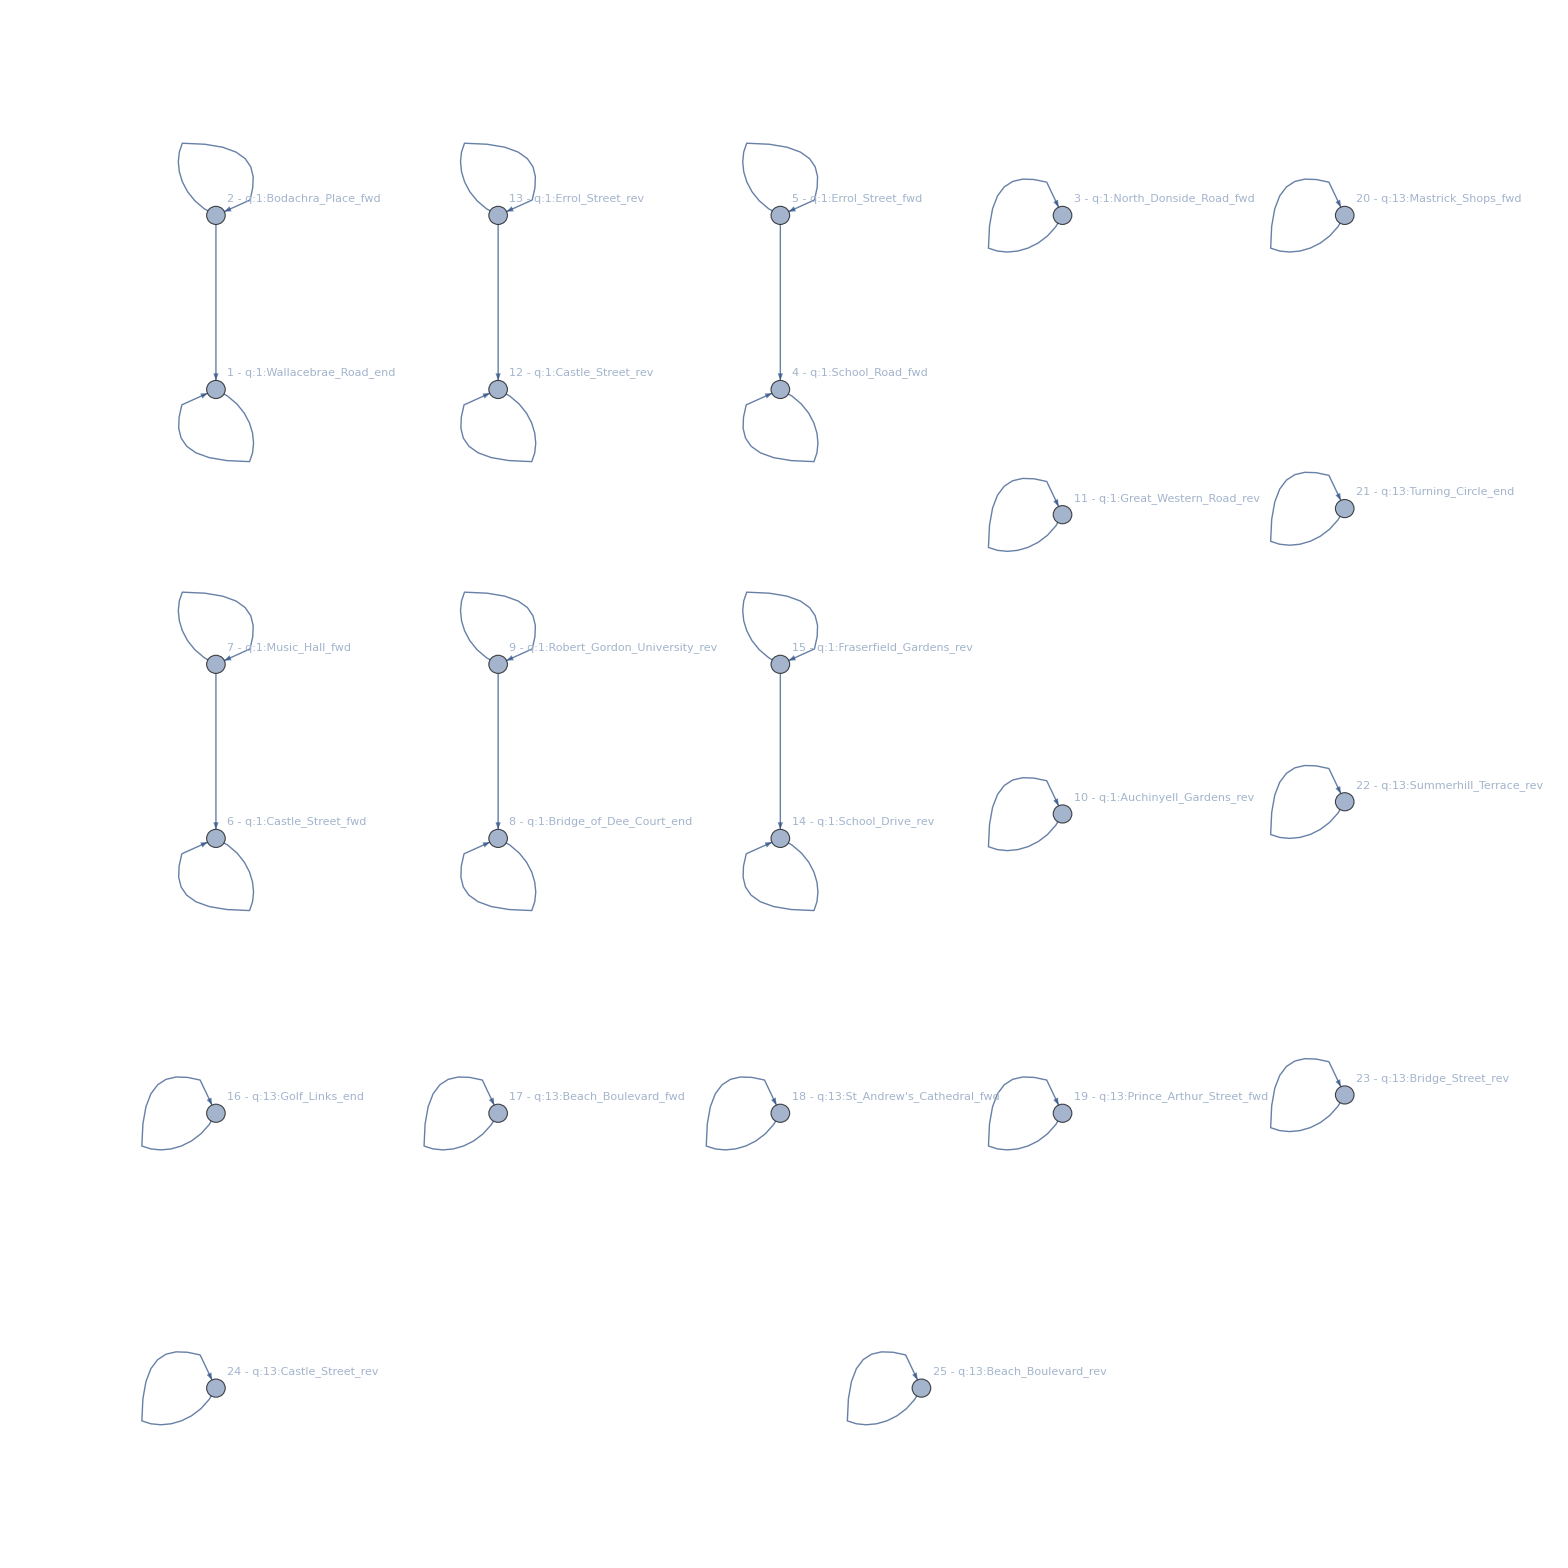

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14.
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 9. | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 6. | -∞)

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞)

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 20. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 12. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 12. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 18. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 12. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 9. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 6. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞)

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]];
```

```mathematica
mtx // MatrixForm
```

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 20. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 27. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 34. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 39. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 44. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 22. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 49. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 27. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 63. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 41. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 67. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 45. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 16. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 27. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 22. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 31. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 26. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 36. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 31. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 43. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 38. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 47. | -∞ | -∞ | -∞ | -∞ | -∞ | 64. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 42. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 57. | -∞ | -∞ | -∞ | -∞ | -∞ | 74. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 52. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 67. | -∞ | -∞ | -∞ | -∞ | -∞ | 84. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 62. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 24. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 27. | -∞ | -∞ | -∞ | -∞ | -∞ | 44. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 22. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞ | -∞ | 50. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 28. | -∞ | -∞ | -∞)

```mathematica
ExportMaxPlusMatrix["matrix1-13", mtx]
```

E:\Dokumentumok\Uni\2023-II\MX4553\Project\maxplusbus\matrix1-13.hdf

```mathematica
Dimensions[mtx]
```

{25,25}

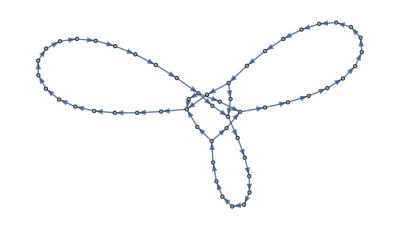

```mathematica
Graph[TAPs[[2]]]
```

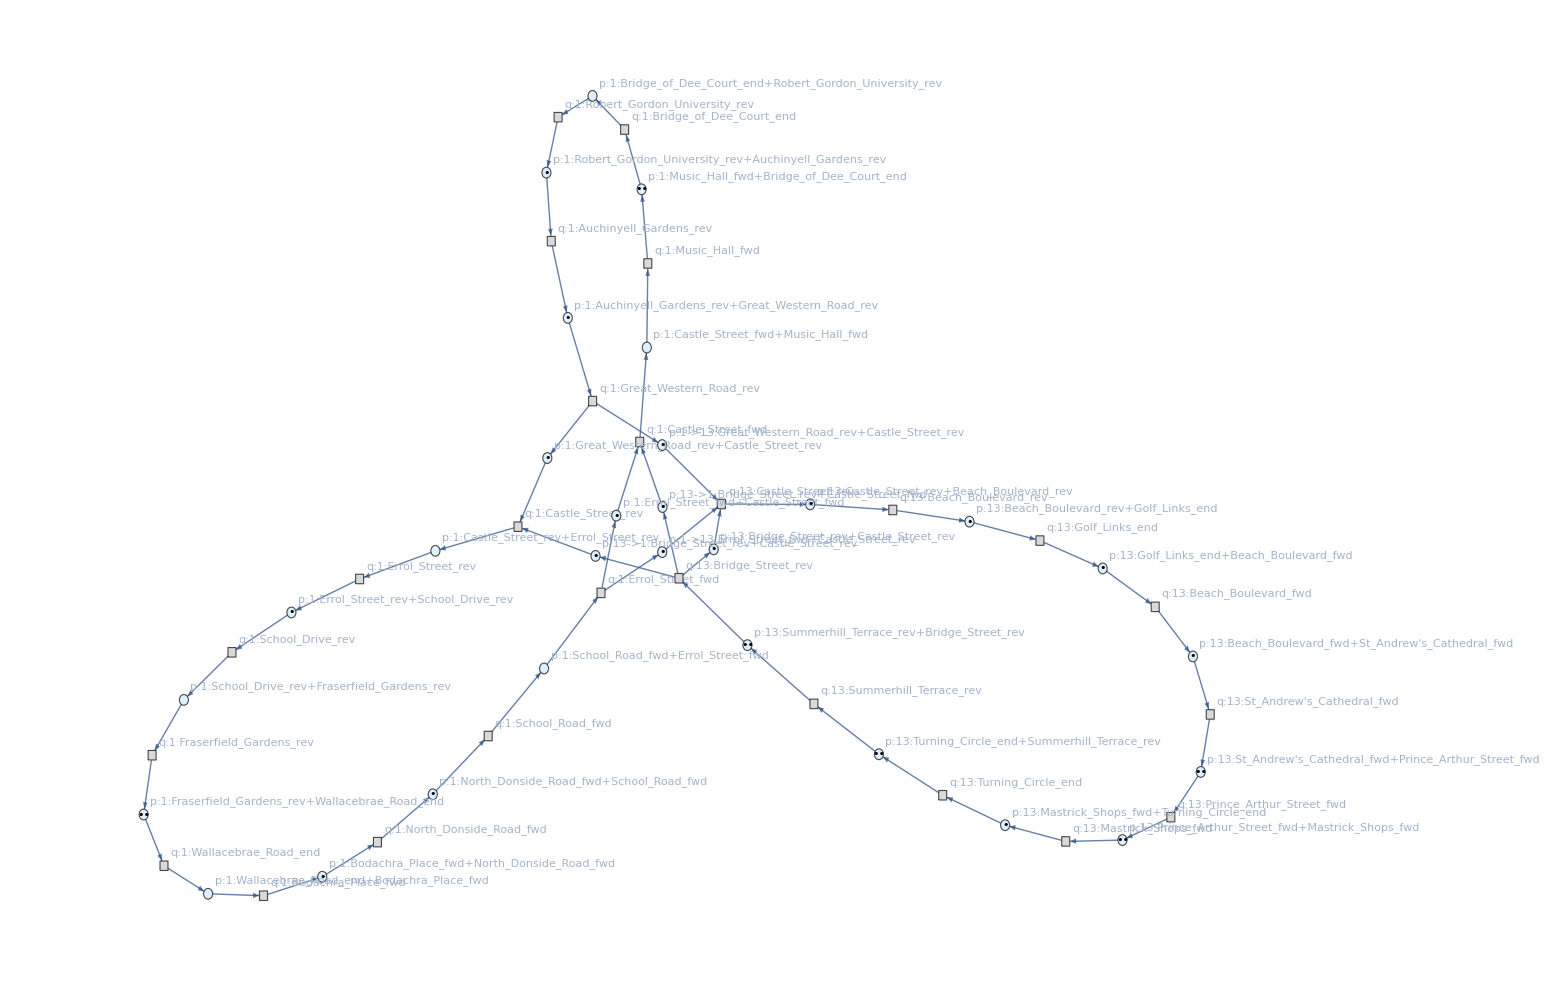

```mathematica
placesList=Keys[TAPs[[3]]];
transitionsList=TAPs[[1]];
arcsList=TAPs[[2]];
initialMarkings=#[[2]]&/@Values[TAPs[[3]]];
petriNet=ResourceFunction["MakePetriNet"][placesList,transitionsList,arcsList, initialMarkings];
petriNet["LabeledGraph"]
```

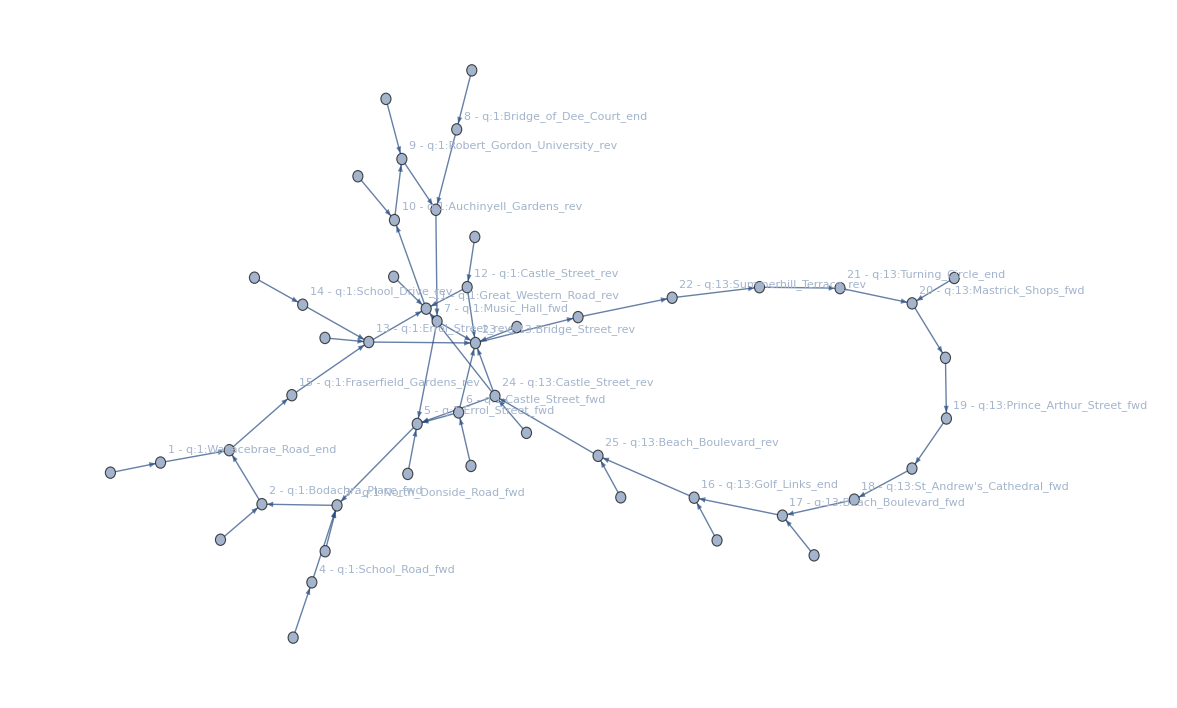

```mathematica
ReplaceInRows[matrix_,oldValue_,newValue_]:=Replace[matrix,oldValue->newValue,{2}]
ChangeNonZeroValues[matrix_,newValue_]:=matrix/. x_/;x!=eps:>newValue
noZeros = ChangeNonZeroValues[mtx, 1];
noInfi = ReplaceInRows[noZeros, -eps, 0] ;
AdjacencyGraph[noInfi, {VertexLabels->Table[i->StringJoin[ToString[i], " - ",TAPs[[1]][[i]]],{i,1,25}]}]
```

```mathematica
mtx //MatrixForm
```

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 20. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 12. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 12. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 18. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 8. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 12. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 9. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 5. | -∞ | -∞ | -∞ | -∞ | -∞ | 11. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 7. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 6. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 0 | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞)

```mathematica
Length[TAPs[[1]]]
```

135

```mathematica
Max[initialMarkings]
```

1

```mathematica
mtx2 =ReplaceInRows[mtx, eps, -1]
```

```mathematica
Max[#]& /@ Transpose[mtx2]
```

{-1,-1,-1,-1,-1,-1,-1,-1,1359.,-1,-1,-1,-1,-1,1347.,-1,-1,-1,-1,-1,-1,-1,1372.,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1358.,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1360.,-1,-1,-1,-1,-1,-1,1368.,1366.,-1,-1,-1,13.,24.,-1,15.,1365.,-1,-1,-1,-1,-1,-1,15.,15.,6.,15.,1369.,-1,-1,-1,-1,-1,-1,-1,-1,-1,1359.,-1,-1,-1,-1,-1,-1,-1,1353.,-1,-1,-1,-1,-1,-1,1366.,-1,-1,-1,-1,1351.,1357.,-1,1367.,-1,-1,28.,-1,-1,-1,1365.,-1,-1,-1,27.,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1366.,-1,-1,-1,-1,-1}

```mathematica
TAPs[[1]][[#]]& /@List[1,10,11,24,36,99,107,105,95,79,131,78,96,93,77,112,111,110,80,94,92,81,55,2,114,82,85,84,60,86]
```

{q:1:Wallacebrae_Road_end,q:1:Auchinyell_Gardens_rev,q:1:Great_Western_Road_rev,q:2:Great_Western_Road_rev,q:3:Aberdeen_Royal_Infirmary_rev,q:18:Redmoss_Road_end,q:19:Mannofield_Church_fwd,q:19:Culter_end,q:18:Mugiemoss_Road_fwd,q:17:Howes_Road_fwd,q:23:Hilton_Drive_rev,q:17:Newhills_fwd,q:18:Powis_Lane_fwd,q:18:Dyce_end,q:17:Riverview_Drive_fwd,q:19:Tillydrone_end,q:19:St_George's_Church_fwd,q:19:Sir_Duncan_Rice_Library_fwd,q:17:Mugiemoss_Road_fwd,q:18:Riverview_Drive_fwd,q:17:Cloverfield_Gardens_rev,q:17:Millbank_Place_fwd,q:12:Chestnut_Row_rev,q:1:Bodachra_Place_fwd,q:19:Broad_Street_rev,q:17:Bon_Accord_Centre_fwd,q:17:Faulds_Gate_end,q:17:Abbotswell_School_fwd,q:13:Mastrick_Shops_fwd,q:17:Devanha_Gardens_rev}